```mathematica
(* Copyright (C) 2020 Craciun Alexandru

This package is free: you can redistribute it and/or modify it under the
 terms of the GNU General Public License as published by the Free Software
 Foundation, either version 3 of the License, or (at your option) any
 later version. This program is distributed in the hope that it will be
 useful, but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General
 Public License for more details. You should have received a copy of the
 GNU General Public License along with this program
if not, see <https://www.gnu.org/licenses/>.

 Author: CRACIUN Alexandru, e-mail:alexandru.craciun@inflpr.ro

 Please send me an e-mail if you have found a mistake or have questions. *)
(*This program/package will be periodically updated.*)
(*Project repository:
https://github.com/DeathMetal/Wave-Propagation-Mathematica *)

(*This code is compatible with Mathematica 10 or later versions.*)

(*Mathematica is (C) Copyright 1988-2020 Wolfram Research, Inc. 
Protected by copyright law and international treaties. 
Unauthorized reproduction or distribution subject to severe civil and criminal penalties.
Mathematica is a registered trademark of Wolfram Research, Inc. 
*)
```

```mathematica
(*These are the custom Color Functions that come with this program. *)
```

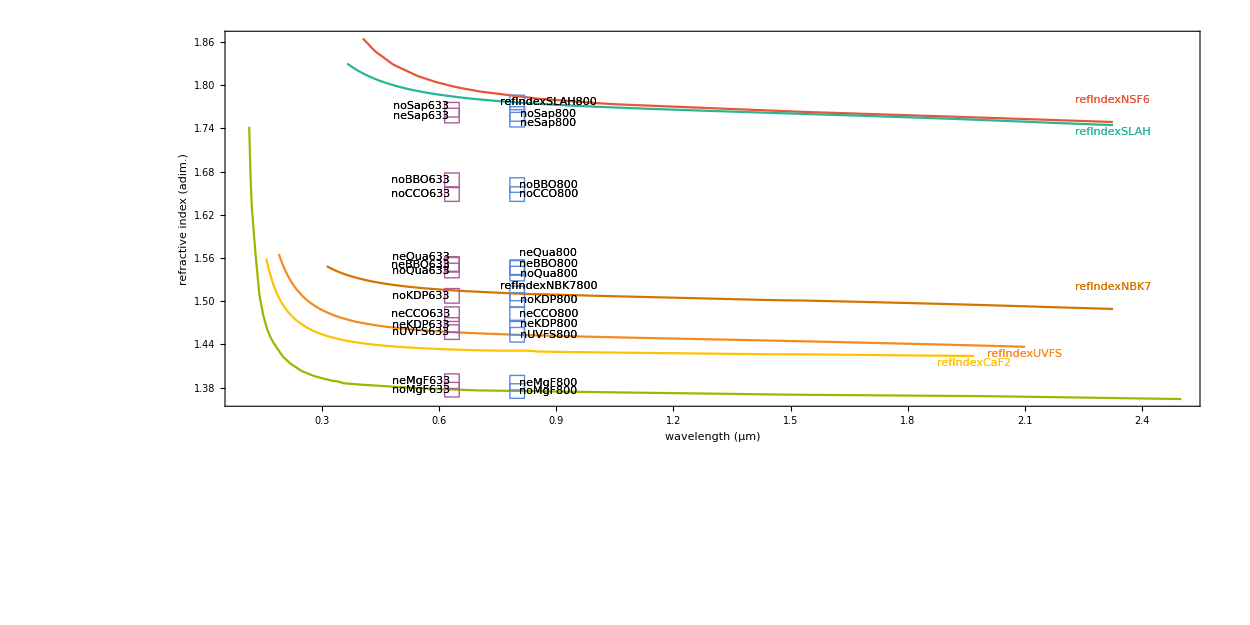
```mathematica
(*---------------------------------------------------------------------------------------------------------------------*)

(*These values of refractive index for the most common optical glasses and birefringent materials are defined. *)
-Graphics-
```

```mathematica
(* Special Instructions *)
SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontWeight->Plain,FontColor->Darker[Red],ShowAutoStyles->False,ShowSyntaxStyles->False,AutoNumberFormatting->False,FontFamily->"Consolas"}}]
```

```mathematica
Off[InterpolatingFunction::dmval]

(* Constants *)
um=                  10^(-6);
mm=                  10^(-3);
waveLength=0.8 um;
(*waveLength=0.532 um;*)
(*Select your main wavelength here.*)
k0=                  2*Pi/waveLength;
Protect[um,mm,k0,waveLength];
(*---------------------------------------------------------------------------------------------------------------------*)

(* Refractive Index for various materials. *)
refIndexNBK7800=1.5108;(* N-BK7 @ 800 nm from https://refractiveindex.info/?shelf=glass&book=BK7&page=SCHOTT .*)
refIndexSLAH800=1.7761;(*S-LAH64 @ 800 nm from https://refractiveindex.info/?shelf=glass&book=OHARA-LAH&page=S-LAH64 .*)
(*Here is the refractive index for the medium between components. *)
refIndexAirTab={1.0003128650267126,(*- source Optica Software*)
1.0002824469995648,1.0002738810151126,
1.0002701958763696,1.0002682603645856,
1.0002671145835633,1.0002663791983342,
1.000265878696659,1.000265522494052,
1.000265259898407,1.000265060708263,
1.000264906006238,1.0002647834467842,
1.000264684692264,1.0002646039456309,
1.000264537074204,1.0002644810670525,
1.0002644336882403,1.0002643932490562,
1.00026435845473};
refIndexAirTab=Transpose[{Table[i,{i,0.2 um,2.1 um,0.1 um}],refIndexAirTab}];
refIndexAirFun=Interpolation[refIndexAirTab,InterpolationOrder->6];
refIndexAir=refIndexAirFun[waveLength];(*The refractive index is evaluated at the working wavelength.*)

(*@ 800 nm from https://refractiveindex.info:   *)
noKDP800=1.5015;(*Potassium Dideuterium Phosphate (KDP), ordinary index *)
neKDP800=1.4633;(*Potassium Dideuterium Phosphate (KDP), extraordinary index *)
noBBO800=1.6614;(*β-Barium Borate (BBO), ordinary index *)
neBBO800=1.5462;(*β-Barium Borate (BBO), extraordinary index *)
noMgF800=1.3751;(*Magnesiun Flouride, ordinary index *)
neMgF800=1.3867;(*Magnesiun Flouride, extraordinary index *)
noQua800=1.5383;(*Crystal Quartz, ordinary index *)
neQua800=1.5472;(*Crystal Quartz, extraordinary index *)
noSap800=1.76013;(*Sapphire, ordinary index *)
neSap800=1.7522;(*Sapphire, extraordinary index *)
nUVFS800=1.4533;(*Ultra-Violet Grade Fused Silica *)
noCCO800=1.6488;(*Calcite, ordinary index *)
neCCO800=1.4819;(*Calcite, extraordinary index *)
(*@ 633 nm from https://refractiveindex.info:   *)
noKDP633=1.5074;(*Potassium Dideuterium Phosphate (KDP), ordinary index *)
neKDP633=1.4669;(*Potassium Dideuterium Phosphate (KDP), extraordinary index *)
noBBO633=1.6680;(*β-Barium Borate (BBO), ordinary index *)
neBBO633=1.5506;(*β-Barium Borate (BBO), extraordinary index *)
noMgF633=1.3770;(*Magnesiun Flouride, ordinary index *)
neMgF633=1.3888;(*Magnesiun Flouride, extraordinary index *)
noQua633=1.5426;(*Crystal Quartz, ordinary index *)
neQua633=1.5516;(*Crystal Quartz, extraordinary index *)
noSap633=1.7660;(*Sapphire, ordinary index *)
neSap633=1.7579;(*Sapphire, extraordinary index *)
nUVFS633=1.4570;(*Ultra-Violet Grade Fused Silica *)
noCCO633=1.6488;(*Calcite, ordinary index *)
neCCO633=1.4819;(*Calcite, extraordinary index *)

refIndexNSF6Fun=Interpolation[{{4.047*^-7,1.86506},{4.358*^-7,1.84738},{4.800*^-7,1.8298},{4.861*^-7,1.82783},{5.461*^-7,1.81266},{5.876*^-7,1.80518},{5.893*^-7,1.80491},{6.328*^-7,1.79883},{6.428*^-7,1.79749},{6.563*^-7,1.79608},{7.065*^-7,1.79114},{8.521*^-7,1.78144},{1.0140*^-6,1.77486},{1.0600*^-6,1.77341},{1.5296*^-6,1.76307},{1.9701*^-6,1.75541},{2.3254*^-6,1.74895}},InterpolationOrder->6];
refIndexNSF6=refIndexNSF6Fun[waveLength];(* https://shop.schott.com/medias/SCHOTT-datasheet-N-SF6.pdf?context=bWFzdGVyfHJvb3R8NDgyODE3fGFwcGxpY2F0aW9uL3BkZnxoMjIvaGRkLzg4MjI1NjQ3ODIxMTAucGRmfDk3YmIyMzgwMWFlMjk4NDYxOWRkYzdmZTM2MmNkNmM0NjQwM2VkNWIxYThiYmI4MzlhMDg3ZDUzYTRiMmI0YWE *)

refIndexNBK7Fun=Interpolation[{{3.126*^-7,1.54862},{3.341*^-7,1.54272},{3.650*^-7,1.53627},{4.047*^-7,1.53024},{4.358*^-7,1.52668},{4.800*^-7,1.52283},{4.861*^-7,1.52238},{5.461*^-7,1.51872},{5.876*^-7,1.5168},{5.893*^-7,1.51673},{6.328*^-7,1.51509},{6.438*^-7,1.51472},{6.563*^-7,1.51432},{7.065*^-7,1.51289},{8.521*^-7,1.5098},{1.0140*^-6,1.50731},{1.0600*^-6,1.50669},{1.5296*^-6,1.50091},{1.9701*^-6,1.49495},{2.3254*^-6,1.48921}},InterpolationOrder->6];
refIndexNBK7=refIndexNBK7Fun[waveLength]; (*https://shop.schott.com/medias/schott-datasheet-n-bk7-eng.pdf?context=bWFzdGVyfHJvb3R8NjkxODAwfGFwcGxpY2F0aW9uL3BkZnxoZTUvaDM4Lzg4MTAzMTYxMDM3MTAucGRmfGJjNmI4ZjFmY2Q1NjMxMTE0MjkzMTUwOGRmMTUzOTg2NWJjZTgzMjA0OTc2NTNiMThjN2RhMjI4NGZmMWM4MWU *)

refIndexUVFSFun=Interpolation[{{1.900*^-7,1.56572},{2.000*^-7,1.55051},{2.139*^-7,1.53431},{2.267*^-7,1.52275},{2.302*^-7,1.52008},{2.399*^-7,1.51337},{2.483*^-7,1.50840},{2.652*^-7,1.50003},{2.753*^-7,1.49591},{2.803*^-7,1.49404},{2.894*^-7,1.49099},{2.967*^-7,1.48873},{3.022*^-7,1.48719},{3.303*^-7,1.48054},{3.404*^-7,1.47858},{3.511*^-7,1.47671},{3.611*^-7,1.47513},{3.650*^-7,1.47454},{4.047*^-7,1.46962},{4.358*^-7,1.46669},{4.416*^-7,1.46622},{4.579*^-7,1.46498},{4.765*^-7,1.46372},{4.861*^-7,1.46313},{4.880*^-7,1.46301},{4.965*^-7,1.46252},{5.145*^-7,1.46156},{5.320*^-7,1.46071},{5.461*^-7,1.46008},{5.876*^-7,1.45846},{5.893*^-7,1.45840},{6.328*^-7,1.45702},{6.438*^-7,1.45670},{6.563*^-7,1.45637},{6.943*^-7,1.45542},{7.065*^-7,1.45515},{7.860*^-7,1.45356},{8.200*^-7,1.45298},{8.300*^-7,1.45282},{8.521*^-7,1.45247},{9.040*^-7,1.45170},{1.0140*^-6,1.45024},{1.0640*^-6,1.44963},{1.1000*^-6,1.44920},{1.2000*^-6,1.44805},{1.3000*^-6,1.44692},{1.4000*^-6,1.44578},{1.5000*^-6,1.44462},{1.5500*^-6,1.44402},{1.6600*^-6,1.44267},{1.7000*^-6,1.44217},{1.8000*^-6,1.44087},{1.9000*^-6,1.43951},{2.0000*^-6,1.43809},{2.1000*^-6,1.43659}},InterpolationOrder->6];
refIndexUVFS=refIndexUVFSFun[waveLength];(* https://www.cvilaseroptics.com/media/wysiwyg/cms-pages/pdf/material_properties.pdf *)

refIndexCaF2Fun=Interpolation[{{1.5763*^-7,1.55927},{1.9300*^-7,1.501804},{2.4830*^-7,1.46793},{2.8040*^-7,1.458251},{2.9673*^-7,1.454649},{3.1257*^-7,1.451744},{3.3415*^-7,1.448497},{3.6501*^-7,1.444893},{4.0466*^-7,1.441490},{4.3583*^-7,1.439470},{4.8000*^-7,1.437272},{4.8613*^-7,1.437014},{5.4607*^-7,1.434932},{5.8756*^-7,1.433843},{5.8930*^-7,1.433803},{6.3280*^-7,1.432882},{6.4385*^-7,1.432676},{6.5627*^-7,1.432455},{7.0652*^-7,1.431667},{8.5211*^-7,1.430024},{1.01398*^-6,1.428795},{1.06000*^-6,1.428506},{1.52958*^-6,1.426115},{1.97009*^-6,1.423965}},InterpolationOrder-> 6];
refIndexCaF2=refIndexCaF2Fun[waveLength];(* http://www.yuanch.com/pdf/fhg.pdf *)

refIndexMgF2Fun=Interpolation[{{1.14*^-7,1.742},{1.17*^-7,1.68},{1.19*^-7,1.651},{1.21*^-7,1.628},{1.30*^-7,1.566},{1.40*^-7,1.509},{1.50*^-7,1.48},{1.60*^-7,1.461},{1.70*^-7,1.448},{1.8*^-7,1.439},{1.90*^-7,1.431},{2.00*^-7,1.423},{2.20*^-7,1.413},{2.48*^-7,1.403},{2.57*^-7,1.401},{2.66*^-7,1.399},{2.80*^-7,1.396},{3.00*^-7,1.393},{3.30*^-7,1.389},{3.37*^-7,1.389},{3.50*^-7,1.387},{3.55*^-7,1.386},{4.00*^-7,1.384},{5.46*^-7,1.379},{7.00*^-7,1.376},{1.087*^-6,1.373},{1.512*^-6,1.370},{2.000*^-6,1.368},{2.500*^-6,1.364},{3.030*^-6,1.36},{3.571*^-6,1.354},{4.000*^-6,1.349},{4.546*^-6,1.341},{5.000*^-6,1.334},{5.569*^-6,1.324},{6.060*^-6,1.314}},InterpolationOrder->6];
refIndexMgF2=refIndexMgF2Fun[waveLength];(* https://www.crystran.co.uk/optical-materials/magnesium-fluoride-mgf2 *)

refIndexSLAHFun=Interpolation[{{3.65015*^-7,1.83016},{4.04656*^-7,1.81666},{4.35835*^-7,1.80888},{4.4157*^-7,1.80765},{4.8000*^-7,1.8006},{4.8613*^-7,1.79963},{5.4607*^-7,1.79196},{5.8756*^-7,1.78800},{5.89290*^-7,1.78785},{6.32800*^-7,1.78453},{6.43850*^-7,1.78379},{6.56270*^-7,1.78300},{7.06520*^-7,1.78018},{7.68190*^-7,1.77737},{8.52110*^-7,1.77433},{1.01398*^-6,1.76996},{1.12864*^-6,1.76750},{1.52958*^-6,1.76026},{1.97000*^-6,1.75220},{2.32542*^-6,1.74466}},InterpolationOrder-> 6];
refIndexSLAH=refIndexSLAHFun[waveLength];(* https://www.ohara-gmbh.com/fileadmin/user_upload/export-data/pdf/product_datasheets/S-LAH64_English_.pdf *)
(*---------------------------------------------------------------------------------------------------------------------*)

(* Here some custom Color Functions are defined. *)
val1={0,1/9,23/63,13/21,47/63,55/63,1};
val1WP={0,1/63,1/16,1/9,23/63,4/9,11/21,38/63,47/63,55/63, 1};
val2={0,1/6,1/3,1/2,2/3,5/6,1};
val6={0,1/9,23/63,50/103,115/206,13/21,145/206,47/63,55/63,390/421,1};
val7={0,1/5,2/5,1/2,2/3,4/5,1};
valsCD3={0,5/9,2/3,7/9,8/9,1};
valsCD97={0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1};

col1={RGBColor[0, 0, Rational[9, 16]],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[1, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[Rational[1, 2], 0, 0]};

col1WP={RGBColor[Rational[17, 20], Rational[19, 27], Rational[17, 20]],RGBColor[0.5, 0, 0.5],RGBColor[Rational[1, 4], 0, Rational[13, 16]],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[0, Rational[4, 5], 0],RGBColor[1, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[Rational[1, 2], 0, 0]};

col1WO={RGBColor[Rational[19, 27], Rational[659, 864], Rational[17, 20]],RGBColor[0, Rational[51, 256], Rational[51, 128]],RGBColor[Rational[1, 4], 0, Rational[13, 16]],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[0, Rational[4, 5], 0],RGBColor[1, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[Rational[1, 2], 0, 0]};

col2={RGBColor[0, 0, 1],RGBColor[0, Rational[1, 2], 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0]};

col3={RGBColor[0.5, 0, 0.5],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};

col6={RGBColor[Rational[1, 4], 0, Rational[1, 4]],RGBColor[Rational[9, 20], 0, Rational[1, 2]],RGBColor[Rational[4, 5], 0, Rational[3, 5]],RGBColor[0, 0, 1],RGBColor[0, Rational[2, 5], Rational[4, 5]],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[0, Rational[3, 4], 0],RGBColor[1, 1, 0],RGBColor[1, Rational[1, 3], 0],RGBColor[1, 0, 0]};

col7={GrayLevel[0],RGBColor[Rational[1, 5], Rational[1, 5], Rational[1, 5]],RGBColor[Rational[2, 5], Rational[3, 10], Rational[1, 4]],RGBColor[Rational[3, 5], Rational[2, 5], Rational[1, 5]],RGBColor[Rational[4, 5], Rational[2, 5], Rational[1, 2]],RGBColor[Rational[3, 4], Rational[1, 2], Rational[7, 10]],RGBColor[Rational[19, 20], Rational[9, 10], Rational[9, 10]]};

colorData3tab={RGBColor[Rational[2, 255], 0.89, 0.81],RGBColor[Rational[2, 255], Rational[26, 51], Rational[79, 85]],RGBColor[Rational[13, 85], Rational[29, 255], Rational[25, 51]],RGBColor[Rational[8, 17], Rational[67, 255], Rational[149, 255]],RGBColor[Rational[227, 255], Rational[1, 85], Rational[25, 51]],RGBColor[Rational[77, 85], Rational[7, 255], Rational[11, 85]]};

colorData97tab={RGBColor[0, 0, 0],RGBColor[Rational[1281, 2000], Rational[931, 4000], Rational[119, 800]],RGBColor[Rational[1411, 2000], Rational[391, 1000], 0],RGBColor[Rational[21, 25], Rational[109, 200], Rational[459, 4000]],RGBColor[Rational[247, 400], Rational[143, 200], 0],RGBColor[Rational[3, 20], Rational[143, 200], Rational[119, 200]],RGBColor[Rational[29, 80], Rational[109, 200], Rational[17, 20]],RGBColor[Rational[23, 40], Rational[167, 400], Rational[17, 20]],RGBColor[Rational[7093, 10000], Rational[2111, 5000], Rational[1271, 2000]],RGBColor[Rational[1379, 1600], Rational[5827, 10000], Rational[501, 800]],RGBColor[Rational[1949, 2000], Rational[3199, 4000], Rational[611, 800]]};

opticaCF=(Hue[0.65-#^0.5 0.65,1,#^0.5 0.9+0.1]&);(*Similar to Optica's version.*)
opticaCFBright=(Hue[0.65-#^0.5 0.65,#^0.5 0.9+0.1,1]&);(*Similar to Optica's version but Brighter.*)
jetMLVPH[u_?NumericQ]:=Blend[Table[{val1[[i]],col3[[i]]},{i,1,Length[val1]}],u](*Cyclic CF simiar to Matlab version.*)
jetMLV18[u_?NumericQ]:=Blend[Table[{val1[[i]]^1.8,col1[[i]]},{i,1,Length[val1]}],u](*This is MatLab version, modified to highlight low intensity regions.*)
jetMLVWP[u_?NumericQ]:=Blend[Table[{val1WP[[i]],col1WP[[i]]},{i,1,Length[val1WP]}],u](*Rainbow similar with MatLab version.*)
jetMLVWO[u_?NumericQ]:=Blend[Table[{val1WP[[i]],col1WO[[i]]},{i,1,Length[val1WP]}],u](*Another variation starting from MatLab version.*)
jetVLV15[u_?NumericQ]:=Blend[Table[{val2[[i]]^1.5,col2[[i]]},{i,1,Length[val2]}],u](*VirtualLab Fusion version, modified to highlight low intensity regions.*)
ophirCF[u_?NumericQ]:=Blend[Table[{val6[[i]]^2,col6[[i]]},{i,1,Length[val6]}],u](*Similar to Ophir's Beam Profiler version.*)
GBPCF[u_?NumericQ]:=Blend[Table[{val7[[i]]^2,col7[[i]]},{i,1,Length[val7]}],u](*Gray - Brown - Pink *)
colorData3[u_?NumericQ]:=Blend[Table[{valsCD3[[i]]^2,colorData3tab[[i]]},{i,1,Length[valsCD3]}],u](*Similar to Mathematica's ColorData[3].*)
colorData97[u_?NumericQ]:=Blend[Table[{valsCD97[[i]],colorData97tab[[i]]},{i,1,Length[valsCD97]}],u](*Similar to Mathematica's ColorData[97].*)

(* More Color Functions. *)
vals0={0,3/50,23/100,33/100,23/50,53/100,3/5,73/100,83/100,9/10,1};
vals1={0,3/10,2/5,1/2,3/5,7/10,4/5,9/10,24/25,1};
vals6={0,1/10,23/100,3/10,9/25,1/2,14/25,63/100,7/10,19/25,24/25,1};

cololrs0={RGBColor[Rational[43, 64], Rational[9, 10], 1],RGBColor[{Rational[79, 128], Rational[49, 128], 1}],RGBColor[{Rational[51, 256], Rational[17, 256], Rational[127, 128]}],RGBColor[{Rational[3, 128], Rational[1, 4], Rational[47, 64]}],RGBColor[{Rational[13, 64], Rational[243, 256], Rational[5, 128]}],RGBColor[{Rational[139, 256], Rational[127, 128], 0}],RGBColor[{Rational[109, 128], Rational[237, 256], 0}],RGBColor[{Rational[255, 256], Rational[57, 128], 0}],RGBColor[{Rational[61, 64], Rational[29, 256], 0}],RGBColor[{Rational[189, 256], Rational[3, 256], 0}],RGBColor[{Rational[33, 128], 0, 0}]};

cololrs2={RGBColor[Rational[1, 8], 0, 0],RGBColor[Rational[7, 9], 0, 0],RGBColor[Rational[25, 26], Rational[1, 12], 0],RGBColor[1, Rational[5, 16], 0],RGBColor[1, Rational[7, 12], 0],RGBColor[1, Rational[11, 13], Rational[1, 79]],RGBColor[1, Rational[43, 44], Rational[1, 5]],RGBColor[1, 1, Rational[4, 7]],RGBColor[1, 1, Rational[9, 11]],RGBColor[1, 1, Rational[8, 9]]};

cololrs2b={RGBColor[0, Rational[1, 12], 0],RGBColor[0, Rational[11, 14], 0],RGBColor[Rational[1, 18], 1, 0],RGBColor[Rational[5, 16], 1, 0],RGBColor[Rational[10, 17], 1, 0],RGBColor[Rational[6, 7], 1, 0],RGBColor[1, 1, Rational[1, 6]],RGBColor[1, 1, Rational[4, 7]],RGBColor[1, 1, Rational[5, 6]],RGBColor[1, 1, Rational[20, 21]]};

cololrs3={RGBColor[Rational[1, 10], 0, Rational[1, 8]],RGBColor[Rational[1, 12], Rational[1, 5], Rational[9, 14]],RGBColor[Rational[1, 44], Rational[5, 13], Rational[4, 9]],RGBColor[Rational[1, 40], Rational[10, 19], Rational[2, 7]],RGBColor[Rational[1, 22], Rational[7, 11], Rational[1, 7]],RGBColor[Rational[3, 11], Rational[3, 4], Rational[1, 21]],RGBColor[Rational[7, 10], Rational[4, 5], Rational[1, 10]],RGBColor[Rational[19, 20], Rational[6, 7], Rational[3, 5]],RGBColor[1, Rational[11, 12], Rational[7, 8]],RGBColor[1, Rational[16, 17], Rational[12, 13]]};

cololrs4={RGBColor[Rational[1, 14], Rational[1, 38], Rational[1, 8]],RGBColor[Rational[3, 8], 0, Rational[10, 13]],RGBColor[Rational[7, 11], 0, Rational[9, 14]],RGBColor[Rational[11, 13], Rational[1, 8], Rational[3, 10]],RGBColor[Rational[12, 13], Rational[6, 17], Rational[2, 9]],RGBColor[Rational[20, 21], Rational[7, 13], Rational[1, 5]],RGBColor[Rational[12, 13], Rational[8, 11], Rational[1, 7]],RGBColor[Rational[15, 16], Rational[7, 8], Rational[2, 5]],RGBColor[Rational[30, 31], Rational[14, 15], Rational[5, 7]],RGBColor[Rational[46, 47], Rational[20, 21], Rational[5, 6]]};

cololrs5={RGBColor[{Rational[3, 64], Rational[1, 32], Rational[17, 256]}],RGBColor[{Rational[31, 256], Rational[47, 128], Rational[17, 64]}],RGBColor[{Rational[19, 64], Rational[59, 128], Rational[53, 256]}],RGBColor[{Rational[73, 128], Rational[61, 128], Rational[71, 256]}],RGBColor[{Rational[197, 256], Rational[127, 256], Rational[67, 128]}],RGBColor[{Rational[207, 256], Rational[19, 32], Rational[203, 256]}],RGBColor[{Rational[197, 256], Rational[97, 128], Rational[119, 128]}],RGBColor[{Rational[209, 256], Rational[231, 256], Rational[241, 256]}],RGBColor[{Rational[115, 128], Rational[123, 128], Rational[61, 64]}],RGBColor[{Rational[239, 256], Rational[125, 128], Rational[247, 256]}]};

cololrs6={RGBColor[0, 0, 0],RGBColor[{0, Rational[3, 128], Rational[39, 64]}],RGBColor[{0, Rational[139, 256], Rational[125, 128]}],RGBColor[{0, Rational[111, 128], Rational[109, 128]}],RGBColor[{Rational[1, 128], Rational[63, 64], Rational[65, 128]}],RGBColor[{Rational[107, 256], Rational[127, 128], Rational[1, 64]}],RGBColor[{Rational[101, 128], Rational[233, 256], 0}],RGBColor[{Rational[31, 32], Rational[161, 256], 0}],RGBColor[{Rational[255, 256], Rational[65, 256], Rational[7, 128]}],RGBColor[{1, Rational[11, 256], Rational[77, 256]}],RGBColor[{1, Rational[11, 256], Rational[11, 16]}],RGBColor[{1, Rational[3, 4], Rational[255, 256]}]};

spectralCF[u_?NumericQ]:=Blend[Table[{vals0[[i]]^1.2,cololrs0[[i]]},{i,1,Length[vals0]}],u]
hotCF[u_?NumericQ]:=Blend[Table[{vals1[[i]]^2,cololrs2[[i]]},{i,1,Length[vals1]}],u]
radioactiveCF[u_?NumericQ]:=Blend[Table[{vals1[[i]]^2,cololrs2b[[i]]},{i,1,Length[vals1]}],u]
kindlCF[u_?NumericQ]:=Blend[Table[{vals1[[i]]^2,cololrs3[[i]]},{i,1,Length[vals1]}],u]
plasmaCF[u_?NumericQ]:=Blend[Table[{vals1[[i]]^2,cololrs4[[i]]},{i,1,Length[vals1]}],u]
cubehelixCF[u_?NumericQ]:=Blend[Table[{vals1[[i]]^2,cololrs5[[i]]},{i,1,Length[vals1]}],u]
beamprofilerCF2[u_?NumericQ]:=Blend[Table[{vals6[[i]]^1.4,cololrs6[[i]]},{i,1,Length[vals6]}],u](*Many beam profilers use something similar to this CF.*)
(*---------------------------------------------------------------------------------------------------------------------*)

(* Here are some options for plotting. *)SetOptions[ListLinePlot,Frame->True,Axes->False,ImageSize->785,AspectRatio->1,FrameStyle->Directive[Darker[Darker[Gray]],39,Thick],ImagePadding->{{165,35},{165,35}},PlotStyle->Thick,FrameLabel->{"r (μm)","Intensity (arb.units)"},LabelStyle->{{FontSize->39,FontFamily->"Cambria",Black}}];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->785,AspectRatio->1,FrameStyle->Directive[Darker[Darker[Gray]],39,Thick],ImagePadding->{{165,35},{165,35}},PlotStyle->Thick,FrameLabel->{"r (μm)","Intensity (arb.units)"},LabelStyle->{FontSize->39,FontFamily->"Cambria",Black}];
SetOptions[Plot,Frame->True,Axes->False,ImageSize->785,AspectRatio->1,FrameStyle->Directive[Darker[Darker[Gray]],39,Thick],ImagePadding->{{165,35},{165,35}},PlotStyle->Thick,FrameLabel->{"r (μm)","Intensity (arb.units)"},LabelStyle->{FontSize->39,FontFamily->"Cambria",Black}];
SetOptions[DensityPlot,ImageSize->785,AspectRatio->1,FrameStyle->Directive[Darker[Darker[Gray]],39,Thick],ImagePadding->{{165,35},{165,35}},FrameLabel->{"x (μm)","y (μm)"},LabelStyle->{FontSize->39,FontFamily->"Cambria",Black},PlotRangePadding->0,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->39,FontFamily->"Cambria",Black},LegendMarkerSize->554.5],ColorFunction-> ophirCF];
SetOptions[ListDensityPlot,ImageSize->785,AspectRatio->1,FrameStyle->Directive[Darker[Darker[Gray]],39,Thick],ImagePadding->{{165,35},{165,35}},FrameLabel->{"x (μm)","y (μm)"},LabelStyle->{FontSize->39,FontFamily->"Cambria",Black},PlotRangePadding->0,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->39,FontFamily->"Cambria",Black},LegendMarkerSize->554.5],ColorFunction-> ophirCF];
(* SetOptions[ListPointPlot3D,ColorFunction->(spectralCF[#3]&),BoxRatios->{1, 1, 0.005},ImageSize->785,AspectRatio->1,LabelStyle->{FontSize->39,FontFamily->"Cambria",Black},PlotRangePadding->0,ColorFunctionScaling->False,ViewPoint->Top,PlotStyle->PointSize[0.01],ImagePadding->{{165,35},{165,35}},AxesLabel->{"x (μm)","y (μm)",""},AxesStyle->Directive[Darker[Darker[Gray]],39,Thick],BoxStyle->Directive[Darker[Darker[Gray]],39,Thick]]; *)
(*---------------------------------------------------------------------------------------------------------------------*)

(* Definitions *)
(*     - Typical interface functions *)
SLz[x_,y_,R_,Ck_]=               (x^2+y^2)/R/(1+Sqrt[1-(1+Ck)*(x^2+y^2)/R^2]);(*Standard surface; x y -> input coordinates, R -> Radius of curvature, Ck -> Conical constant. *)
Axz[x_,y_,R_,Al_]=                 R+SLz[x,y,R*Cot[Al/180.*Pi]^2,-1-Cot[Al/180.*Pi]^2];(*Rounded tip axicon with tip radius R; x y -> input coordinates, R -> Radius of curvature of the tip, Al -> Axicon's angle. *)
ALz[x_,y_,R_,Ck_,coef_]=(x^2+y^2)/R/(1+Sqrt[1-(1+Ck)*(x^2+y^2)/R^2])+Dot[{#^1,#^2,#^3,#^4,#^5,#^6,#^7,#^8}&@(x^2/mm^2+y^2/mm^2),coef] mm;
(*Even aspherical surface; x y -> input coordinates, R -> Radius of curvature, Ck -> Conical constant, coef -> aspherical surface coefficients. *)
OAP[x_,y_,R_,x0_]=            -(((x-x0)^2+y^2)/(2 R));

(*     - Typical transmission functions *)
(*Singular Phase Dislocation and related functions. *)
Tλ[θ_,λ0λ_,m_Integer]:=Exp[ⅈ λ0λ Mod[m θ, 2π]-ⅈ π λ0λ];(*Transmission function of a sectional SPP designed for λ0 that is illumitated with wavelength λ (λ0λ = λ0/λ); θ -> azimuthal angle, m -> topological charge of the SPP. *)
TλFourier[θ_,λ0λ_,m_Integer,kMax_Integer]:=(Sin[π λ0λ]/π)∑_(k=-kMax)^kMax Exp[ⅈ k m θ]/(λ0λ-k);(*Tλ is decomposed in Fourier Series. Tλ as sum of vortex modes with indices between -kMax and kMax. *)
TN[θ_,λ0λ_,m_Integer,Ν_Integer]:=Exp[ⅈ λ0λ Mod[m (Floor[Ν θ, 2 π]/Ν),2 π]-ⅈ π λ0λ+ⅈ π (m/Ν)];(* Transmission function of a sectional Diffractive SPP designed for λ0 with N steps(i.e. N/m discrete levels). *)
TNFourier[θ_,m_Integer,Ν_Integer,kMax_Integer]:=-Ν *(Sin[π m/Ν]/π)∑_(k=-kMax)^kMax Exp[ⅈ(m-Ν k) θ]/(m-Ν k);(*TN is decomposed in Fourier Series. TN as sum of vortex modes with indices between -kMax and kMax. *)
TλFourier[θ_,λ0λ_,m_Integer,kList_List]:=(Sin[π λ0λ]/π)Sum[Exp[ⅈ k m θ]/(λ0λ-k),{k,kList}];(*Summation of certain vortex modes with indices included in the list kList with the Fourier coefficients of Tλ. *)

TNFourier[θ_,m_Integer,Ν_Integer,kList_List]:=-Ν *(Sin[π m/Ν]/π)Sum[Exp[ⅈ(m-Ν k) θ]/(m-Ν k),{k,kList}];(*Summation of certain vortex modes with indices included in the list kList with the Fourier coefficients of TN. *)
(*     - Miscelaneous*)
(*Not yet defined.*)

(*     - Grids of parallel rays*)
CartesianGrid[rad_,num_Integer]  :=Flatten[Table[{x,y},{x,-N@rad,rad,2 rad/(num-1.)},{y,-N@rad,rad,2 rad/(num-1.)}],1];
(*rad -> the spatial extent of the rays bundle, num -> related to the number of rays. *)

(*The version without chief-ray is more suitable when we deal with singular beams with the singularity along the chief-ray. *)
Options[HexapolarGrid]={"chiefRay"-> True};
HexapolarGrid[rad_,num_Integer,OptionsPattern[]] :=If[OptionValue["chiefRay"]==True,
Join[{{0,0}},Flatten[Table[p rad/num{Cos[th],Sin[th]},{p,1,num},{th,2 Pi/(6. p), 2Pi,2 Pi/(6. p)}],1]],
Flatten[Table[p rad/num{Cos[th],Sin[th]},{p,1,num},{th,2 Pi/(6. p), 2Pi,2 Pi/(6. p)}],1]];
(*rad -> the spatial extent of the rays bundle, num -> related to the number of rays. *)

LineGrid[rad_,num_Integer]            :=Table[{x,0},{x,-N@rad,rad,2 rad/(num-1.)}]; (*Useful for graphics or optimization of circularly symmetric optical systems. *)
(*rad -> the spatial extent of the rays bundle, num -> the number of rays. *)

CircleGrid[rad_,num_Integer]       :=Table[rad{Cos[th],Sin[th]},{th,2 N@Pi/num,2 Pi,2 N@Pi/num}];(*rad -> distance from the optica axis of the rays bundle, num -> the number of rays. *)
(*---------------------------------------------------------------------------------------------------------------------*)


(*     - Functions needed for system optimization*)

FindFocus[surfaceCoordinates_List,rayTilt_List]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,tx,ty,tz},

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

-Total[(rx*tx+ry*ty)/tz]/Total[(tx^2+ty^2)/tz^2]

](*This function return the position of the focal plane with respect to the plane on which surfaceCoordinates and rayTilt are defined. *)


Options[FindFocusGaussian]={"radius"-> 1 mm};(*The option "radius" is the radius of the Gaussian beam at 1/e^2. *)
FindFocusGaussian[surfaceCoordinates_List,rayTilt_List,OptionsPattern[]]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,tx,ty,tz,W},
W=OptionValue["radius"];

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

-Total[Exp[-2(rx^2+ry^2)/W^2]*(rx*tx+ry*ty)/tz]/Total[Exp[-2(rx^2+ry^2)/W^2]*(tx^2+ty^2)/tz^2]

](*This function return the position of the focal plane with respect to the plane on which surfaceCoordinates and rayTilt are defined, 
assuming that rays carry a certain energy that changes according to a Gaussian function with respect to the optical axis. *)


FindFocusLine[surfaceCoordinates_List,rayTilt_List]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,tx,ty,tz,W},

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

-Total[√(rx^2+ry^2)*(rx*tx+ry*ty)/tz]/Total[√(rx^2+ry^2)*(tx^2+ty^2)/tz^2]

](*This function return the position of the focal plane with respect to the plane on which surfaceCoordinates and rayTilt are defined,
assuming a line grid of rays. The energy carried by the rays increase linearly with the distance from the optical axis to
simulate a circular beam. *)


FindDivergence[rayTilt_List]:=Module[{ta=Transpose@rayTilt,tx,ty},

tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];

ArcSin[Sqrt[Total[(tx^2+ty^2)]/Length[tx]]]

](*This function return the geometrically computed divergence of the beam.*)

Options[FindDivergenceGaussian]={"radius"-> 1 mm};(*The option "radius" is the radius of the Gaussian beam at 1/e^2. *)
FindDivergenceGaussian[surfaceCoordinates_List,rayTilt_List,OptionsPattern[]]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,tx,ty,W},
W=OptionValue["radius"];

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];
(*Preferable to use the input coordinates for surfaceCoordinates.*)
ArcSin[Sqrt[Total[(tx^2+ty^2)Exp[-2(rx^2+ry^2)/W^2]]/Total[Exp[-2(rx^2+ry^2)/W^2]]] ]

](*This function return the geometrically computed divergence of the beam,
assuming that rays carry a certain amount of energy that changes according to a Gaussian function with the distance from the optical axis. *)

FindDivergenceLine[surfaceCoordinates_List,rayTilt_List]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,tx,ty},

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];
(*Preferable to use input coordinates for surfaceCoordinates.*)
Sqrt[Total[(tx^2+ty^2)Sqrt[rx^2+ry^2]]/Total[Sqrt[rx^2+ry^2]]]

](*This function return the geometrically computed divergence of the beam,
assuming that rays carry a certain amount of energy that changes linearly with the distance from the optical axis.*)

FindSpotSize[surfaceCoordinates_List,rayTilt_List]:=Module[{sc=Transpose@surfaceCoordinates,ta=Transpose@rayTilt,rx,ry,rz,tx,ty,tz},

rx=sc[[1]];(*surfaceCoordinates -> input coordinates of the rays, *)
ry=sc[[2]];
tx=ta[[1]];(*rayTilt            -> input direction vectors.*)
ty=ta[[2]];

If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];
rz=-Total[(rx*tx+ry*ty)/tz]/Total[(tx^2+ty^2)/tz];(*This part compute the positon of the focal plane in the same way as FindFocus.*)
rx=rx+rz*tx/tz;
ry=ry+rz*ty/tz;

Sqrt[Total[rx^2+ry^2]/Length[rx]]

](*This function return the geometrically computed focal spot size. *)

(*FindSpotSizeGaussian, FindSpotSizeLine - will be defined in the further versions. *)
(*---------------------------------------------------------------------------------------------------------------------*)

(* Ray Tracing Functions - Parallel Version*)

(*Here is an exemplification of the method used to find the intersection of the rays with the surface. *)

(*-Graphics- with derivatives known, 2 iterations are needed to find the intersection. *)
(*-Graphics-without knowing the derivatives, 4 or more are iterations needed to find the intersection. *)
SurfaceIntersection[prevRayCoordinate_List,Z_List,rayTilt_List][surface_,DxSurface_,DySurface_]:=Module[{sc=Transpose@prevRayCoordinate,ta=Transpose@rayTilt,S,k,rx,ry,rz,tx,ty,tz},
rx=sc[[1]];(*prevRayCoordinate -> input coordinates of the rays or the coordinates resulted from the previous iteration, *)
ry=sc[[2]];(*Z -> a list with z coordinates of the rays.*)
If[Length[sc]≥ 3,rz=sc[[3]],rz=Z];(*z coordinate is needed, prevRayCoordinate should contain the z coordinate, in this case the variable Z is ignored. Otherwise a list Z is expected.*)
tx=ta[[1]];(*rayTilt            -> input direction vectors of the rays.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

ParallelMap[(
S=surface[#[[1]],#[[2]]]-#[[3]];(*surface -> the surface function (must be a function of two variables),*)
k=DxSurface[#[[1]],#[[2]]]*#[[4]]+DySurface[#[[1]],#[[2]]]*#[[5]];(*DxSurface DySurface -> derivatives of the surface with respect to x and y.*)
{#[[1]],#[[2]],#[[3]]}+{#[[4]],#[[5]],#[[6]]}*S/(#[[6]]-k))&,Transpose[{rx,ry,rz,tx,ty,tz}]
,Method-> "CoarsestGrained"]

](*This function return the coordinates x, y, z of the intersection between the ray bundle and the surface "surface". When the derivatives "DxSurface", "DySurface"are given, the method used is similar to Newton-Raphson.
If the derivatives are not known analythical, write 0& instead. This function should be used in a Do loop, each iteration increases the accuracy.
This method is exact in 1 iteration the for intersection between tilted rays and a plane surface or the intersection between rays parallel to the optical axis and a non-planar surface. *)

(*"refractiveIndexMedium" refers to the medium in which the material is immersed, for example, the option "refractiveIndexMedium"-> 1.5 is a good way to model an optical component in water. *)
Options[DirectionIn]={"refractiveIndexMedium"-> refIndexAir};
DirectionIn[prevRayCoordinate_List,rayTilt_List,refractiveIndex_?NumericQ,OptionsPattern[]][DxSurface_,DySurface_]:=Module[{refractiveIndexMedium,sc=Transpose@prevRayCoordinate,ta=Transpose@rayTilt,nD,tr,tDot,Dx,Dy,rx,ry,rz,tx,ty,tz},
refractiveIndexMedium=OptionValue["refractiveIndexMedium"];

rx=sc[[1]];(*prevRayCoordinate -> input coordinates of the rays, *)
ry=sc[[2]];

tx=ta[[1]];(*rayTilt            -> input direction vectors of the rays.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

ParallelMap[(
Dx=DxSurface[#[[1]],#[[2]]];(*DxSurface DySurface -> derivatives of the surface with respect to x and y.*)
Dy=DySurface[#[[1]],#[[2]]];
nD={-Dx,-Dy,1}/Sqrt[1+Dx^2+Dy^2];

tr={#[[3]],#[[4]],#[[5]]};
tDot=Dot[nD,tr];
tr=nD*Sqrt[1-(refractiveIndexMedium/refractiveIndex)^2*(1-tDot^2)]+(tr-nD*tDot)*(refractiveIndexMedium/refractiveIndex);(*refractiveIndex -> refractive index of the optical component.*)
tr=tr/Norm[tr])&,Transpose[{rx,ry,tx,ty,tz}]
,Method-> "CoarsestGrained"]

](*This function return the direction vector {tx, ty, tz} of the rays refracted from the surface, assuming that light enter in the component. 
This function uses the vectorial form of Snell law of refraction. For reflection use the value -refractiveIndexMedium as refractiveIndex. *)

Options[DirectionOut]={"refractiveIndexMedium"-> refIndexAir};(*"refractiveIndexMedium" -> refractive index of the medium in which the material is immersed.*)
DirectionOut[prevRayCoordinate_List,rayTilt_List,refractiveIndex_?NumericQ,OptionsPattern[]][DxSurface_,DySurface_]:=Module[{refractiveIndexMedium,sc=Transpose@prevRayCoordinate,ta=Transpose@rayTilt,nD,tr,tDot,Dx,Dy,rx,ry,rz,tx,ty,tz},
refractiveIndexMedium=OptionValue["refractiveIndexMedium"];

rx=sc[[1]];(*prevRayCoordinate -> input coordinates of the rays, *)
ry=sc[[2]];

tx=ta[[1]];(*rayTilt            -> input direction vectors of the rays.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

ParallelMap[(
Dx=DxSurface[#[[1]],#[[2]]];(*DxSurface DySurface -> derivatives of the surface with respect to x and y.*)
Dy=DySurface[#[[1]],#[[2]]];
nD={-Dx,-Dy,1}/Sqrt[1+Dx^2+Dy^2];

tr={#[[3]],#[[4]],#[[5]]};
tDot=Dot[nD,tr];
tr=nD*Sqrt[1-(refractiveIndex/refractiveIndexMedium)^2*(1-tDot^2)]+(tr-nD*tDot)*(refractiveIndex/refractiveIndexMedium);(*refractiveIndex -> refractive index of the optical component.*)
tr=tr/Norm[tr])&,Transpose[{rx,ry,tx,ty,tz}]
,Method-> "CoarsestGrained"]

](*This function return the direction vector {tx, ty, tz} of the rays refracted from the surface, assuming that light exits the component. 
This function uses the vectorial form of Snell law of refraction. For reflection use the value -refractiveIndex as refractiveIndex. *)

DirectionIn[prevRayCoordinate_List,rayTilt_List,refractiveIndex_List,OptionsPattern[]][DxSurface_,DySurface_]:=Module[{refractiveIndexMedium,sc=Transpose@prevRayCoordinate,ta=Transpose@rayTilt,nD,tr,tDot,Dx,Dy,rx,ry,rz,tx,ty,tz},
refractiveIndexMedium=OptionValue["refractiveIndexMedium"];

rx=sc[[1]];(*prevRayCoordinate -> input coordinates of the rays, *)
ry=sc[[2]];

tx=ta[[1]];(*rayTilt            -> input direction vectors of the rays.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

ParallelMap[(
Dx=DxSurface[#[[1]],#[[2]]];(*DxSurface DySurface -> derivatives of the surface with respect to x and y.*)
Dy=DySurface[#[[1]],#[[2]]];
nD={-Dx,-Dy,1}/Sqrt[1+Dx^2+Dy^2];

tr={#[[3]],#[[4]],#[[5]]};
tDot=Dot[nD,tr];
tr=nD*Sqrt[1-(refractiveIndexMedium/#[[6]])^2*(1-tDot^2)]+(tr-nD*tDot)*(refractiveIndexMedium/#[[6]]);
tr=tr/Norm[tr])&,Transpose[{rx,ry,tx,ty,tz,refractiveIndex}](*refractiveIndex -> refractive index of the optical component, here refractiveIndex is a table equal in length with prevRayCoordinate and rayTilt.*)
,Method-> "CoarsestGrained"]

](*This function return the direction vector {tx, ty, tz} of the rays refracted from the surface, assuming that light enter in the component. *)
(* This works with a different refractive index for each ray. Good for modeling of anisotropic media. *)

DirectionOut[prevRayCoordinate_List,rayTilt_List,refractiveIndex_List,OptionsPattern[]][DxSurface_,DySurface_]:=Module[{refractiveIndexMedium,sc=Transpose@prevRayCoordinate,ta=Transpose@rayTilt,nD,tr,tDot,Dx,Dy,rx,ry,rz,tx,ty,tz},
refractiveIndexMedium=OptionValue["refractiveIndexMedium"];

rx=sc[[1]];(*prevRayCoordinate -> input coordinates of the rays, *)
ry=sc[[2]];

tx=ta[[1]];(*rayTilt            -> input direction vectors of the rays.*)
ty=ta[[2]];
If[Length[ta]≥ 3,tz=ta[[3]],tz=Sqrt[1-(tx^2+ty^2)]];

ParallelMap[(
Dx=DxSurface[#[[1]],#[[2]]];(*DxSurface DySurface -> derivatives of the surface with respect to x and y.*)
Dy=DySurface[#[[1]],#[[2]]];
nD={-Dx,-Dy,1}/Sqrt[1+Dx^2+Dy^2];

tr={#[[3]],#[[4]],#[[5]]};
tDot=Dot[nD,tr];
tr=nD*Sqrt[1-(#[[6]]/refractiveIndexMedium)^2*(1-tDot^2)]+(tr-nD*tDot)*(#[[6]]/refractiveIndexMedium);
tr=tr/Norm[tr])&,Transpose[{rx,ry,tx,ty,tz,refractiveIndex}](*refractiveIndex -> refractive index of the optical component, here refractiveIndex is a table equal in length with prevRayCoordinate and rayTilt.*)
,Method-> "CoarsestGrained"]

](*This function return the direction vector {tx, ty, tz} of the rays refracted from the surface, assuming that light exits the component. *)
(* This works with a different refractive index for each ray. Good for modeling of anisotropic media. *)

Options[FindOpticalPathLength]={"waveLength"-> waveLength,"returnHistogram"-> False};(*"waveLength" -> wavelenght of the radiation used, "returnHistogram" -> returns a histogram of the list carring the values of optical length for each ray. *)
FindOpticalPathLength[intersection_List,refractiveIndexs_,OptionsPattern[]]:=Module[{lambda,k0,opticalLength},
lambda=OptionValue["waveLength"];
k0=2 Pi/lambda;
opticalLength=Table[(intersection[[i+1]]-intersection[[i]])*refractiveIndexs[[i]],{i,1,Length[intersection]-1}];
(*intersection -> a list of lists with the coordinates of the intersection with each surface, Ex. {{coords. intersection surface1},{coords. intersection surface1}, ... } *)
opticalLength=Total[Map[√(#[[1]]^2+#[[2]]^2+#[[3]]^2)&,opticalLength,{2}]];
(*refractiveIndexs -> a list of refractive indexes of each medium. Length[refractiveIndexs]+1 == Length[intersection] *)
If[OptionValue["returnHistogram"]== True,Print[Histogram[k0 (opticalLength-Min[opticalLength])mm]]];
opticalLength
](* This function gives the optical path length along a ray.*)

Options[FindOpticalPathLengthU]={"waveLength"-> waveLength,"returnHistogram"-> False};
FindOpticalPathLengthU[intersection_List,refractiveIndexs_,OptionsPattern[]]:=Module[{lambda,k0,opticalLength},
lambda=OptionValue["waveLength"];
k0=2 Pi/lambda;
opticalLength=Table[Map[#[[1]]*#[[2]]&,Transpose[{(intersection[[i+1]]-intersection[[i]]),refractiveIndexs[[i]]}]],{i,1,Length[intersection]-1}];
(*intersection -> a list of lists with the coordinates of the intersection with each surface, Ex. {{coords. intersection surface1},{coords. intersection surface1}, ... } *)
opticalLength=Total[Map[√(#[[1]]^2+#[[2]]^2+#[[3]]^2)&,opticalLength,{2}]];
(*refractiveIndexs -> a list of lists with the refractive index for each ray. Length[refractiveIndexs]+1 == Length[intersection] and Length[refractiveIndexs[[i]]] == Length[intersection[[j]]] for all i, j *)
If[OptionValue["returnHistogram"]== True,Print[Histogram[k0 (opticalLength-Min[opticalLength])mm]]];
opticalLength
](* This function gives the optical path length along a ray, considering a different refractive index for each ray. *)


(*Rotations *)
Options[RotationX]={"units"-> "grad"};(*"units" -> units for angles, could be "grad" or "rad". Is expected that for "units" -> "rad" to use integer/half integer/ so on multiple of π, in this way exact results and simplifications are perimtted. 
For "units" -> "grad", angle is numericized. *)
RotationX[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{1, 0, 0}, {0, Cos[a], -Sin[a]}, {0, Sin[a], Cos[a]}});(*angle -> the angle of rotation, *)
Map[#.matrix&,list](*          list -> the list of 3D coordinates on which rotation is applied. *)

](*This function roatates a list of coordinates around axis X. *)
Options[InverseRotationX]={"units"-> "grad"};
InverseRotationX[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{1, 0, 0}, {0, Cos[a], Sin[a]}, {0, -Sin[a], Cos[a]}});
Map[#.matrix&,list]

](*This function roatates a list of coordinates around axis X in the opposite sense compared with RotationX. *)
Options[RotationY]={"units"-> "grad"};
RotationY[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], 0, -Sin[a]}, {0, 1, 0}, {Sin[a], 0, Cos[a]}});
Map[#.matrix&,list]

](*This function roatates a list of coordinates around axis Y. *)
Options[InverseRotationY]={"units"-> "grad"};
InverseRotationY[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], 0, Sin[a]}, {0, 1, 0}, {-Sin[a], 0, Cos[a]}});
Map[#.matrix&,list]

](*This function roatates a list of coordinates around axis Y in the opposite sense compared with RotationY. *)
Options[RotationZ]={"units"-> "grad"};
RotationZ[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], -Sin[a], 0}, {Sin[a], Cos[a], 0}, {0, 0, 1}});
Map[#.matrix&,list]

](*This function roatates a list of coordinates around axis Z. *)
Options[InverseRotationZ]={"units"-> "grad"};
InverseRotationZ[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], Sin[a], 0}, {-Sin[a], Cos[a], 0}, {0, 0, 1}});
Map[#.matrix&,list]

](*This function roatates a list of coordinates around axis Z in the opposite sense compared with RotationZ. *)

Options[RotationAxis]={"units"-> "grad"};
RotationAxis[angle_,direction_,list_,OptionsPattern[]]:=Module[{matrix,a,ux,uy,uz},(*direction -> direction vector around which rotation is performed. *)
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
{ux,uy,uz}=direction/Norm[direction];
matrix=({{Cos[a]+ux^2 (1-Cos[a]), ux uy (1-Cos[a])-uz Sin[a], ux uz (1-Cos[a])+uy Sin[a]}, {uy ux (1-Cos[a])+uz Sin[a], Cos[a]+uy^2 (1-Cos[a]), uy uz (1-Cos[a])-ux Sin[a]}, {uz ux (1-Cos[a])-uy Sin[a], uz uy (1-Cos[a])+ux Sin[a], Cos[a]+uz^2 (1-Cos[a])}});
Map[#.matrix&,list]

](*This function rotates a list of coordinates around an arbitrary axis defned by the direction vector direction = {ux, uy, uz}, in the opposite sense compared with RotationAxis. *)
Options[InverseRotationAxis]={"units"-> "grad"};
InverseRotationAxis[angle_,direction_,list_,OptionsPattern[]]:=Module[{matrix,a,ux,uy,uz},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a]+ux^2 (1-Cos[a]), ux uy (1-Cos[a])+uz Sin[a], ux uz (1-Cos[a])-uy Sin[a]}, {uy ux (1-Cos[a])-uz Sin[a], Cos[a]+uy^2 (1-Cos[a]), uy uz (1-Cos[a])+ux Sin[a]}, {uz ux (1-Cos[a])+uy Sin[a], uz uy (1-Cos[a])-ux Sin[a], Cos[a]+uz^2 (1-Cos[a])}});
Map[#.matrix&,list]

](*This function rotates a list of coordinates around an arbitrary axis defned by the direction vector direction = {ux, uy, uz}. *)
(*Improper Rotations *)
Options[ReflexionX]={"units"-> "grad"};
ReflexionX[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{1, 0, 0}, {0, Cos[a], Sin[a]}, {0, Sin[a], -Cos[a]}});
Map[#.matrix&,list]

]
Options[ReflexionY]={"units"-> "grad"};
ReflexionY[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], 0, Sin[a]}, {0, 1, 0}, {Sin[a], 0, -Cos[a]}});
Map[#.matrix&,list]

]
Options[ReflexionZ]={"units"-> "grad"};
ReflexionZ[angle_,list_,OptionsPattern[]]:=Module[{matrix,a},
a=If[OptionValue["units"]=="grad",Pi/180. *angle,angle];
matrix=({{Cos[a], Sin[a], 0}, {Sin[a], -Cos[a], 0}, {0, 0, 1}});
Map[#.matrix&,list]

(*ReflexionAxis...will be finished in the next versions.*)

]

(* Geometric Propagation Operators *)
(* If 4th param is present, represent wavelength in μm, in not present the wavelength is that defined at the beginning. *)
(*The interpolation order is restricted to 1 for hexagonal or other non-uniform grids.*)
Options[GeometricOperator]={"InterpolationOrder"-> 6,"uniformGrid"-> False,"curvatureRadius"->0};
(*"InterpolationOrder" -> the interpolation order of the interpolation functions for optical path length and *)
GeometricOperator[rayCS_List,rayCE_List,rayOL_List,OptionsPattern[]][f_]:=Module[{interpolationOrder,rayCoordinateStart,rayCoordinateEnd,opticalLength,opticalLengthMean,mesh,meshE,area,areaE,index,indexE,sqRD,sqRDEnd,X,Y,S,x,y,cR,return},
interpolationOrder=OptionValue["InterpolationOrder"];
If[OptionValue["uniformGrid"]==False,interpolationOrder=1];
cR=OptionValue["curvatureRadius"];


rayCoordinateStart=Map[#[[{1,2}]]&,rayCS];
rayCoordinateEnd=Map[#[[{1,2}]]&,rayCE];
opticalLengthMean=Mean[opticalLength];
mesh=VoronoiMesh[rayCoordinateStart];
area=PropertyValue[{mesh,2},MeshCellMeasure];
index=Flatten@Nearest[rayCoordinateStart->Automatic]@PropertyValue[{mesh,2},MeshCellCentroid];
rayCoordinateStart=rayCoordinateStart[[index]];

sqRD=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateStart,area}],InterpolationOrder->1,"ExtrapolationHandler"->{1&,"WarningMessage"->False}];
meshE=VoronoiMesh[rayCoordinateEnd];
areaE=PropertyValue[{meshE,2},MeshCellMeasure];
indexE=Flatten@Nearest[rayCoordinateEnd->Automatic]@PropertyValue[{meshE,2},MeshCellCentroid];
sqRDEnd=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateEnd[[indexE]],areaE}],InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}];
rayCoordinateEnd=rayCoordinateEnd[[index]];
opticalLength=rayOL[[index]];

X:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,1]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#1&,"WarningMessage"->False}];
Y:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,2]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#2&,"WarningMessage"->False}];

If[cR==0,
S:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]}&,Transpose[{opticalLength,rayCoordinateStart}]],InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{opticalLengthMean&,"WarningMessage"->True}];

return[x_,y_]=f[X[x,y],Y[x,y]]*Exp[ⅈ k0 S[x,y]]*sqRDEnd[x,y]/sqRD[X[x,y],Y[x,y]];,

S:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]+√(cR^2+(#[[2,1]]^2+#[[2,2]]^2))}&,Transpose[{opticalLength,rayCoordinateStart}]],InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{opticalLengthMean&,"WarningMessage"->True}];

return[x_,y_]=f[X[x,y],Y[x,y]]*Exp[ⅈ k0( S[X[x,y],Y[x,y]]-√(cR^2+(X[x,y]^2+Y[x,y]^2)))]*sqRDEnd[x,y]/sqRD[X[x,y],Y[x,y]]; ];

return
]


GeometricOperator[rayCS_List,rayCE_List,rayOL_List,waveLength_,OptionsPattern[]][f_]:=Module[{interpolationOrder,rayCoordinateStart,rayCoordinateEnd,opticalLength,opticalLengthMean,mesh,meshE,area,areaE,index,indexE,sqRD,sqRDEnd,X,Y,S,x,y,cR,return,k0Local},

interpolationOrder=OptionValue["InterpolationOrder"];
If[OptionValue["uniformGrid"]==False,interpolationOrder=1];
cR=OptionValue["curvatureRadius"];

rayCoordinateStart=Map[#[[{1,2}]]&,rayCS];
rayCoordinateEnd=Map[#[[{1,2}]]&,rayCE];
opticalLengthMean=Mean[opticalLength];
mesh=VoronoiMesh[rayCoordinateStart];
area=PropertyValue[{mesh,2},MeshCellMeasure];
index=Flatten@Nearest[rayCoordinateStart->Automatic]@PropertyValue[{mesh,2},MeshCellCentroid];
k0Local=2 π/waveLength;
rayCoordinateStart=rayCoordinateStart[[index]];

sqRD=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateStart,area}],InterpolationOrder->1,"ExtrapolationHandler"->{1&,"WarningMessage"->False}];
meshE=VoronoiMesh[rayCoordinateEnd];
areaE=PropertyValue[{meshE,2},MeshCellMeasure];
indexE=Flatten@Nearest[rayCoordinateEnd->Automatic]@PropertyValue[{meshE,2},MeshCellCentroid];
sqRDEnd=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateEnd[[indexE]],areaE}],InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}];
rayCoordinateEnd=rayCoordinateEnd[[index]];
opticalLength=rayOL[[index]];

X:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,1]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#1&,"WarningMessage"->False}];
Y:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,2]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#2&,"WarningMessage"->False}];

If[cR==0,
S:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]}&,Transpose[{opticalLength,rayCoordinateStart}]],InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{opticalLengthMean&,"WarningMessage"->True}];

return[x_,y_]=f[X[x,y],Y[x,y]]*Exp[ⅈ k0Local S[x,y]]*sqRDEnd[x,y]/sqRD[X[x,y],Y[x,y]];,

S:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]+√(cR^2+(#[[2,1]]^2+#[[2,2]]^2))}&,Transpose[{opticalLength,rayCoordinateStart}]],InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{opticalLengthMean&,"WarningMessage"->True}];

return[x_,y_]=f[X[x,y],Y[x,y]]*Exp[ⅈ k0Local( S[X[x,y],Y[x,y]]-√(cR^2+(X[x,y]^2+Y[x,y]^2)))]*sqRDEnd[x,y]/sqRD[X[x,y],Y[x,y]]; ];

return

]

(*This propagation operator does not carry the phase difference accumumlated. It is useful for propagation to the focal plane together with scalarRSFOperator.*)
Options[AmplitudeGeometricOperator]={"InterpolationOrder"-> 6,"uniformGrid"-> False};
AmplitudeGeometricOperator[rayCS_List,rayCE_List,OptionsPattern[]][f_]:=Module[{interpolationOrder,rayCoordinateStart,rayCoordinateEnd,mesh,meshE,area,areaE,index,indexE,sqRD,sqRDEnd,X,Y,S,x,y,return},
interpolationOrder=OptionValue["InterpolationOrder"];
If[OptionValue["uniformGrid"]==False,interpolationOrder=1];
rayCoordinateStart=Map[#[[{1,2}]]&,rayCS];
rayCoordinateEnd=Map[#[[{1,2}]]&,rayCE];
mesh=VoronoiMesh[rayCoordinateStart];
area=PropertyValue[{mesh,2},MeshCellMeasure];
index=Flatten@Nearest[rayCoordinateStart->Automatic]@PropertyValue[{mesh,2},MeshCellCentroid];
rayCoordinateStart=rayCoordinateStart[[index]];

sqRD=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateStart,area}],InterpolationOrder->1,"ExtrapolationHandler"->{1&,"WarningMessage"->False}];
meshE=VoronoiMesh[rayCoordinateEnd];
areaE=PropertyValue[{meshE,2},MeshCellMeasure];
indexE=Flatten@Nearest[rayCoordinateEnd->Automatic]@PropertyValue[{meshE,2},MeshCellCentroid];
sqRDEnd=Interpolation[{#[[1,1]],#[[1,2]],Sqrt[1/#[[2]]]}&/@Transpose[{rayCoordinateEnd[[indexE]],areaE}],InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}];
rayCoordinateEnd=rayCoordinateEnd[[index]];

X:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,1]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#1&,"WarningMessage"->False}];
Y:=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1,2]]}&,Transpose[{rayCoordinateStart,rayCoordinateEnd}]],InterpolationOrder->1,"ExtrapolationHandler"->{#2&,"WarningMessage"->False}];

return[x_,y_]=f[X[x,y],Y[x,y]]*sqRDEnd[x,y]/sqRD[X[x,y],Y[x,y]];
return

]

(*Physical Optics*)

Options[FresnelOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 3,"returnSamplingTest"-> False};
FresnelOperator[wFP_,nFP_,distP_,OptionsPattern[]][f_]:=Module[{lambda,padLevel,k0,interpolationOrder,nFPpad,dkx,FP,f0T,fzT,x0,y0,return},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
interpolationOrder=OptionValue["InterpolationOrder"];
nFPpad=nFP*padLevel;
dkx=Pi/(wFP*padLevel);
FP[x0_,y0_]=Exp[ⅈ k0*(x0^2+y0^2)/(2 distP)];

If[OptionValue["returnSamplingTest"]== True,Return[ListLinePlot[N@{Re[#]/Abs[#],Im[#]/Abs[#],Abs[#]/Max[Abs[#]]}&@Table[f[x0,um]*FP[x0,0],{x0,-wFP+2 wFP/nFP,wFP,2 wFP/nFP}],FrameLabel->{"",""},PlotMarkers->"□",ImageSize-> 6000,AspectRatio-> 1/20],Module]

];

f0T:=RotateLeft[ArrayPad[N@Table[f[x0,y0]*FP[x0,y0],{x0,-wFP+2 wFP/nFP,wFP,2 wFP/nFP},{y0,-wFP+2 wFP/nFP,wFP,2 wFP/nFP}],(nFPpad-nFP)/2],{nFPpad/2-1,nFPpad/2-1}];

fzT:=RotateRight[Fourier[f0T],{nFPpad/2-1,nFPpad/2-1}]*4 padLevel wFP^2/(lambda distP nFP);

return[x0_,y0_]=- ⅈ Exp[ⅈ k0 distP]*ListInterpolation[ArrayPad[fzT,-(nFPpad-nFP)/2],{{-dkx*(nFP/2-1),dkx*nFP/2},{-dkx*(nFP/2-1),dkx*nFP/2}}*distP/k0,InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}][-x0,-y0]*FP[x0,y0];
return
]

(*This is experimental - if nrSteps ≠ 1 the function will save Abs@data for Z and X.*)
Options[SPWOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 3,"nrSteps"-> 1,"specklePattern"-> 0,"returnSamplingTest"-> False, "tableForm"-> False};
SPWOperator[wASP_,nASP_,distP_,OptionsPattern[]][f_]:=Module[{lambda,padLevel,k0,interpolationOrder,ASP,nASPpad,FTf,IFT,kx,ky,dkx,x0,y0,nZ,ASPtable,ftable,FTfu,IFTu,XZprop,transmF,i},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
interpolationOrder=OptionValue["InterpolationOrder"];
nZ=OptionValue["nrSteps"];
transmF=OptionValue["InterpolationOrder"];
ASP[kx_,ky_]=Exp[ⅈ distP Sqrt[k0^2-kx^2-ky^2]];
nASPpad=nASP*padLevel;
dkx=Pi/(wASP*padLevel);
ASPtable=N@Table[ASP[kx,ky],{kx,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx},{ky,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx}];
ftable=N@Table[f[x0,y0],{x0,-wASP+2wASP/nASP,wASP,2wASP/nASP},{y0,-wASP+2wASP/nASP,wASP,2wASP/nASP}];

If[OptionValue["specklePattern"]≠ 0,ftable=ftable*Normal@SparseArray[Map[#-> RandomComplex[]&,Transpose[{RandomSample[Range[nASP],OptionValue["specklePattern"]],RandomSample[Range[nASP],OptionValue["specklePattern"]]}]],{nASP,nASP},1]];

If[OptionValue["returnSamplingTest"]== True,Print[ListLinePlot[N@{Re[#]/Abs[#],Im[#]/Abs[#],Abs[#]/Max[Abs[#]]}&@Table[f[x0,um],{x0,-wASP+2 wASP/nASP,wASP,2 wASP/nASP}],FrameLabel->{"",""},PlotMarkers->"□",ImageSize-> 8000,AspectRatio-> 1/20]];
Return[ftable,Module]
];

FTf=RotateRight[Fourier[RotateLeft[ArrayPad[ftable,(nASPpad-nASP)/2],{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];

If[OptionValue["returnSamplingTest"]== "Fourier",
Return[ListLinePlot[N@{Re[#]/Abs[#],Im[#]/Abs[#],Abs[#]/Max[Abs[#]]}&@(Table[ASP[kx,0],{kx,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx}]*FTf[[nASPpad/2]]),FrameLabel->{"",""},PlotMarkers->"□",ImageSize-> 8000,AspectRatio-> 1/20],Module]
];

IFT:=RotateRight[InverseFourier[RotateLeft[FTf*ASPtable,{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];

If[nZ≠ 1,
IFTu=IFT;
XZprop={IFTu[[nASPpad/2]]};
Do[

FTfu=RotateRight[Fourier[RotateLeft[IFTu,{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];
IFTu=RotateRight[InverseFourier[RotateLeft[FTfu*ASPtable,{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];
XZprop=Join[XZprop,{IFTu[[nASPpad/2]]}];

,nZ-1];
Return[ListInterpolation[Abs[XZprop],{{0,(nZ-1)*distP},{-wASP+2wASP/nASPpad,wASP}*padLevel},InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}],Module]
];

ListInterpolation[IFT,{{-wASP+2wASP/nASPpad,wASP},{-wASP+2wASP/nASPpad,wASP}}*padLevel,InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
]


Options[SASPWOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"paraxialF"-> False,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 10,"returnSamplingTest"-> False};
SASPWOperator[wASP_,nASP_,distP_,OptionsPattern[]][f_]:=Module[{lambda,padLevel,k0,paraxialF,interpolationOrder,ASP,FP,paraxialASP,FTf,FTfLens,IFT,nASPpad,z,kx,ky,dkx,x0,y0},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
paraxialF=If[NumberQ[OptionValue["paraxialF"]],OptionValue["paraxialF"],distP];
interpolationOrder=OptionValue["InterpolationOrder"];

FP[x0_,y0_]=Exp[ⅈ k0*(x0^2+y0^2)/(2 paraxialF)];

ASP[kx_,ky_]=Exp[ⅈ distP Sqrt[k0^2-kx^2-ky^2]];

paraxialASP[kx_,ky_]=Exp[ⅈ paraxialF*(kx^2+ky^2)/(2 k0)];

nASPpad=nASP*padLevel;
dkx=Pi/(wASP);

If[OptionValue["returnSamplingTest"]== True,Return[ListLinePlot[N@{Re[#]/Abs[#],Im[#]/Abs[#],Abs[#]/Max[Abs[#]]}&@Table[f[x0,um]*FP[x0,0],{x0,-wASP+2 wASP/nASP,wASP,2 wASP/nASP}],FrameLabel->{"",""},PlotMarkers->"□",ImageSize-> 8000,AspectRatio-> 1/20]],Module];

FTf:=RotateRight[Fourier[RotateLeft[N@Table[f[x0,y0]*FP[x0,y0],{x0,-wASP+2wASP/nASP,wASP,2wASP/nASP},{y0,-wASP+2wASP/nASP,wASP,2wASP/nASP}],{nASP/2-1,nASP/2-1}]],{nASP/2-1,nASP/2-1}];

FTfLens:= ArrayPad[RotateRight[Fourier[RotateLeft[FTf*N@Table[paraxialASP[kx,ky],{kx,-dkx*(nASP/2-1),dkx*nASP/2,dkx},{ky,-dkx*(nASP/2-1),dkx*nASP/2,dkx}],{nASP/2-1,nASP/2-1}]],{nASP/2-1,nASP/2-1}]*4  wASP^2/(ⅈ lambda paraxialF nASP),(nASPpad-nASP)/2];

dkx=Pi/(wASP*padLevel);

If[OptionValue["returnSamplingTest"]== "Fourier",
Return[ListLinePlot[N@{Re[#]/Abs[#],Im[#]/Abs[#],Abs[#]/Max[Abs[#]]}&@(Table[ASP[kx,0]*paraxialASP[kx,0],{kx,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx}]*FTfLens[[nASPpad/2]]),FrameLabel->{"",""},PlotMarkers->"□",ImageSize-> 8000,AspectRatio-> 1/20],Module]
];

IFT:=RotateRight[InverseFourier[RotateLeft[ArrayPad[FTfLens,-(nASPpad-nASP)/2]*Table[ASP[kx,ky]*paraxialASP[kx,ky],{kx,(-wASP+2wASP/nASP)*k0/paraxialF,wASP*k0/paraxialF,2wASP/nASP*k0/paraxialF},{ky,(-wASP+2wASP/nASP)*k0/paraxialF,wASP*k0/paraxialF,2wASP/nASP*k0/paraxialF}],{nASP/2-1,nASP/2-1}]],{nASP/2-1,nASP/2-1}];
dkx=Pi/(wASP);
ListInterpolation[IFT,{{-dkx*(nASP/2-1),dkx*nASP/2},{-dkx*(nASP/2-1),dkx*nASP/2}}*(paraxialF/k0),InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
]



Options[SAFarFieldOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"paraxialF"-> False,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 3};
SAFarFieldOperator[wASP_,nASP_,distP_,OptionsPattern[]][f_]:=Module[
{lambda,padLevel,k0,interpolationOrder,ASP,FP,paraxialASP,FTf,FTfFF,IFT,nASPpad,z,kx,ky,dkx,x0,y0,return},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
interpolationOrder=OptionValue["InterpolationOrder"];


ASP[kx_,ky_]=Exp[ⅈ distP Sqrt[k0^2-kx^2-ky^2]];
FP[x0_,y0_]=Exp[ⅈ k0*(x0^2+y0^2)/(2 distP)];
paraxialASP[kx_,ky_]=Exp[ⅈ distP*(kx^2+ky^2)/(2 k0)];

nASPpad=nASP*padLevel;
dkx=Pi/(wASP);

FTf:=RotateRight[Fourier[RotateLeft[N@Table[f[x0,y0],{x0,-wASP+2wASP/nASP,wASP,2wASP/nASP},{y0,-wASP+2wASP/nASP,wASP,2wASP/nASP}]*4 wASP^2/(ⅈ lambda distP nASP),{nASP/2-1,nASP/2-1}]],{nASP/2-1,nASP/2-1}];

FTfFF:=RotateRight[Fourier[RotateLeft[ArrayPad[FTf,(nASPpad-nASP)/2]*N@Table[ASP[kx,ky]*paraxialASP[kx,ky],{kx,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx},{ky,-dkx*(nASPpad/2-1),dkx*nASPpad/2,dkx}],{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];

IFT:=RotateRight[InverseFourier[RotateLeft[FTfFF*N@Table[FP[x0,y0],{x0,(-wASP+2wASP/nASPpad),wASP,2wASP/nASPpad},{y0,(-wASP+2wASP/nASPpad),wASP,2wASP/nASPpad}],{nASPpad/2-1,nASPpad/2-1}]],{nASPpad/2-1,nASPpad/2-1}];

return[x0_,y0_]=ListInterpolation[IFT,{{-dkx*(nASPpad/2-1),dkx*nASPpad/2},{-dkx*(nASPpad/2-1),dkx*nASPpad/2}}*(distP/k0),InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}][x0,y0]*FP[x0,y0];

return
]

Options[scalarRSFOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"defocusZ"-> 0,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 10};
scalarRSFOperator[rayCoordinateFocus_List,rayTiltFocus_List,opticalLengthFocus_List,clearApRad_,nWDP_,focalDistance_,OptionsPattern[]][f_]:=Module[{interpolationOrder,padLevel,lambda,defocusZ,FTf,nWDPpad,k0,dkx,wWDP,S,sx,sy,EF},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
interpolationOrder=OptionValue["InterpolationOrder"];
defocusZ=OptionValue["defocusZ"];

wWDP=clearApRad/(√(clearApRad^2+focalDistance^2)); 

nWDPpad=nWDP*padLevel;
dkx=Pi/(wWDP*k0);
EF=If[UnsameQ[rayCoordinateFocus,{}]==True,
S=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]}&,Transpose[{opticalLengthFocus-Map[#[[1,1]]*#[[2,1]]+#[[1,2]]*#[[2,2]]&,Transpose@{rayCoordinateFocus,rayTiltFocus}],rayTiltFocus}]],InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}];

N@Table[Exp[ⅈ k0 (S[sx,sy]+√(1-sx^2-sy^2) defocusZ)]f[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)]/(1-sx^2-sy^2)*(1+ⅈ√(1-sx^2-sy^2)/(k0^2 focalDistance)),{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],

N@Table[Exp[ⅈ k0 (focalDistance /√(1-sx^2-sy^2)+√(1-sx^2-sy^2)defocusZ)]f[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)]/(1-sx^2-sy^2)*(1+ⅈ√(1-sx^2-sy^2)/(k0^2 focalDistance)),{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}]
];

FTf=RotateRight[Fourier[RotateLeft[EF,{nWDP/2-1,nWDP/2-1}]],{nWDP/2-1,nWDP/2-1}];

ListInterpolation[ArrayPad[-4 ⅈ clearApRad^2 FTf/(lambda*focalDistance nWDP),(nWDPpad-nWDP)/2],{{-dkx*(nWDPpad/2-1),dkx*nWDPpad/2},{-dkx*(nWDPpad/2-1),dkx*nWDPpad/2}},InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
]
```

```mathematica
Options[scalarRSFOperator]={"waveLength"-> waveLength,"padLevel"-> 1,"defocusZ"-> 0,"refractiveIndexMedium"-> refIndexAir,"InterpolationOrder"-> 10};
scalarRSFOperator[rayCoordinateFocus_List,rayTiltFocus_List,opticalLengthFocus_List,clearApRad_,nWDP_,focalDistance_,OptionsPattern[]][f_]:=Module[{interpolationOrder,padLevel,lambda,defocusZ,FTf,nWDPpad,k0,dkx,wWDP,S,sx,sy,sz,EF},
lambda=OptionValue["waveLength"];
padLevel=OptionValue["padLevel"];
k0=2 Pi/lambda*OptionValue["refractiveIndexMedium"];
interpolationOrder=OptionValue["InterpolationOrder"];
defocusZ=OptionValue["defocusZ"];

wWDP=clearApRad/(√(clearApRad^2+focalDistance^2)); 

nWDPpad=nWDP*padLevel;
dkx=Pi/(wWDP*k0);
EF=If[UnsameQ[rayCoordinateFocus,{}]==True,
S=Interpolation[Map[{#[[2,1]],#[[2,2]],#[[1]]}&,Transpose[{opticalLengthFocus-Map[#[[1,1]]*#[[2,1]]+#[[1,2]]*#[[2,2]]&,Transpose@{rayCoordinateFocus,rayTiltFocus}],rayTiltFocus}]],InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}];

N@Table[sz=√(1-sx^2-sy^2);Exp[ⅈ k0 (S[sx,sy]+sz defocusZ)]f[-sx focalDistance/sz,-sy focalDistance/sz]/sz^2*(1+ⅈ sz/(k0^2 focalDistance)),{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],

N@Table[sz=√(1-sx^2-sy^2);Exp[ⅈ k0 (focalDistance /sz+sz defocusZ)]f[-sx focalDistance/sz,-sy focalDistance/sz]/sz^2*(1+ⅈ sz/(k0^2 focalDistance)),{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}]
];

FTf=RotateRight[Fourier[RotateLeft[EF,{nWDP/2-1,nWDP/2-1}]],{nWDP/2-1,nWDP/2-1}];

ListInterpolation[ArrayPad[-4 ⅈ clearApRad^2 FTf/(lambda*focalDistance nWDP),(nWDPpad-nWDP)/2],{{-dkx*(nWDPpad/2-1),dkx*nWDPpad/2},{-dkx*(nWDPpad/2-1),dkx*nWDPpad/2}},InterpolationOrder->interpolationOrder,"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
]
```